```mathematica
(*Question 2*)
```

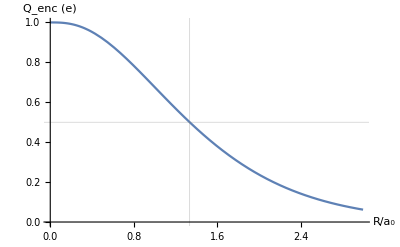

```mathematica
(*2a*)
Plot[{Exp[-2x](2 x^2+2x+1)},{x,0,3},AxesLabel->{"R/a_0","Q_enc (e)"},GridLines->{{1.337},{0.5}}]
```

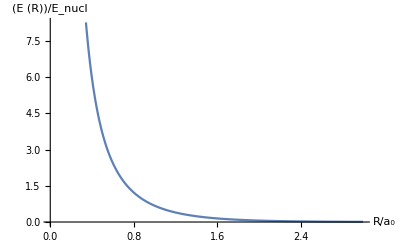

```mathematica
(*2b*)
Plot[{Exp[-2x](2 x^2+2x+1)/x^2},{x,0,3},AxesLabel->{"R/a_0","(E (R))/E_nucl"}]
```

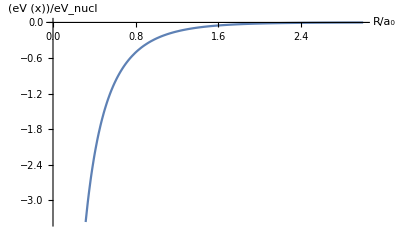

```mathematica
(*2c*)
Plot[{-Exp[-2x*a0](1+a0)/(x*a0)/.a0->1},{x,0,3},AxesLabel->{"R/a_0","(eV (x))/eV_nucl"}]
```

```mathematica
(*Question 3*)
```

```mathematica
Clear["Global`*"]
psi[r_]:=1/(√(π*a0^3))Exp[-Abs[r]/a0];
psiL[r_]=psi[r+b/2];
psiR[r_]=psi[r-b/2];
psiplus[r_]:=Cplus(psiL[r]+psiR[r]);
psiminus[r_]:=Cminus(psiL[r]-psiR[r]);
Cplus=1/(√2)*1/(√(1+S));
Cminus=1/(√2)*1/(√(1-S));
```

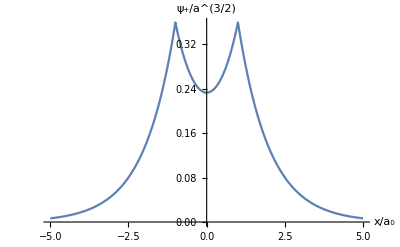

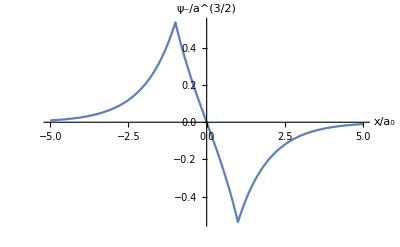

```mathematica
(*3c*)
S=0.586;
b=2.0*a0;
Plot[psiplus[r/a0]/.a0->1,{r,-5,5},AxesLabel->{"x/a_0","ψ_+/a^(3/2)"}]
Plot[psiminus[r/a0]/.a0->1,{r,-5,5},AxesLabel->{"x/a_0","ψ_-/a^(3/2)"}]
```

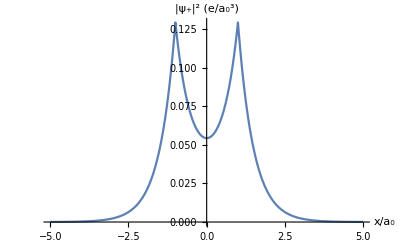

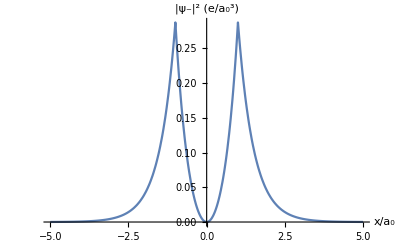

```mathematica
(*3d*)
Plot[psiplus[r/a0]*psiplus[r/a0]/.a0->1,{r,-5,5},AxesLabel->{"x/a_0","|ψ_+|^2 (e/a_0^3)"}]
Plot[psiminus[r/a0]*psiminus[r/a0]/.a0->1,{r,-5,5},AxesLabel->{"x/a_0","|ψ_-|^2 (e/a_0^3)"}]
```

{9,3.02462,1.07857,0.476603,0.211518,0.0770346,0.00497101,-0.0344381,-0.0542245,-0.0632368,-0.0650206,-0.062838,-0.0591423,-0.0540292,-0.0483924,-0.042329,-0.0376367,-0.0320112,-0.0271197,-0.0221839,-0.0187785,-0.0162905,-0.0136929,-0.0104844,-0.00874021}

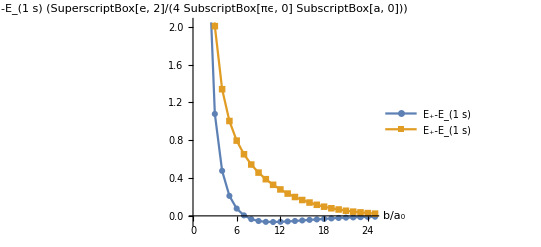

```mathematica
(*3f*)
data=Import["C:\\Users\\pbuttles\\Downloads\\H2_ion,S,J,K_ForHW.csv"];
data=Drop[data,2];
ba0[i_]:=data[[i,1]]
Sdata[i_]:=data[[i,2]]
J[i_]:=data[[i,3]]
K[i_]:=data[[i,4]]
V[i_]:=data[[i,5]]
eplus={};
eminus={};
For[i=1,i<=25,i++,AppendTo[eplus,V[i]+(J[i]+K[i])/(1+Sdata[i])]]
For[i=1,i<=25,i++,AppendTo[eminus,V[i]+(J[i]-K[i])/(1+Sdata[i])]]
eplus
ListLinePlot[{eplus,eminus},PlotLegends->{"E_+-E_(1  s)","E_+-E_(1  s)"},AxesLabel->{"b/a_0","E_±-E_(1  s) (SuperscriptBox[e, 2]/(4 SubscriptBox[πϵ, 0] SubscriptBox[a, 0]))"},PlotMarkers->Automatic]
```

```mathematica
(*Question 4*)
```

```mathematica
(*4b*)
Clear["Global`*"]
Solve[D[-a/rsa0+b/rsa0^2,rsa0]==0,rsa0]
Reduce[{D[D[-a/rsa0+b/rsa0^2,rsa0],rsa0]>0,a>0,b>0},rsa0]
```

{{rsa0→(2 b)/a}}

b>0&&a>0&&(rsa0<0||0<rsa0<(3 b)/a)

```mathematica
(*4c*)
Clear["Global`*"]
alpha=24.35(*eV*);
beta=30.1(*eV*);
rsa0=2beta/alpha
a=4.32(*Å, 10^-10 m*);
a0=0.529(*Å, 10^-10 m*);
Solve[4/3 π*rs^3==a^3/2,rs,Reals];
2.1270492471802243/a0
```

2.47228

4.02089